## supported calculation

```mathematica
(* calculating Subscript[k, on] *)
```

```mathematica
Subscript[k, off]=100;
Subscript[k, d] = 60 10^-9;
Subscript[k, on]=Subscript[k, off]/Subscript[k, d] * 1.7 10^-9
```

2.83333

```mathematica
Print[Style[#,{Blue,Bold,FontSize->16}]&@"K_on:",Subscript[k, on]," ... this is used to compute binding radius"]
```

K_on:2.83333 ... this is used to compute binding radius

```mathematica
(* below is probability generated for a 1st order reaction *)
```

```mathematica
δt = 1 10^-6; (* 1 us time-step *)
Print[Style[#,{Blue,Bold,FontSize->16}]&@"P_dissociation:",1. - Exp[-(Subscript[k, off] δt)]," ... if random number is less than this ligand/receptor complex dissociates"]
```

P_dissociation:0.000099995 ... if random number is less than this ligand/receptor complex dissociates

```mathematica
(* receptor concentration and ligand concentration *)
```

```mathematica
ligandconc = 100 10^-9;
d =(1./(ligandconc * 6 10^23))^(1/3); (* dm *)
Print[Style[#,{Blue,Bold,FontSize->14}]&@"spacing between ligands: ",d* 1 10^8," nm"] (* dm -> nm *)
```

spacing between ligands: 255.436 nm

```mathematica
receptorconc = 40 10^-6;
d =(1/(receptorconc * 6 10^23))^(1/3.); (* dm *)
Print[Style[#,{Blue,Bold,FontSize->14}]&@"spacing between receptors: ",d* 1 10^8," nm"];(* dm -> nm *)
```

spacing between receptors: 34.6681 nm

```mathematica
(* how many ligands and receptors in the simulation box *)
```

```mathematica
Print[Style[#,{Blue,Bold,FontSize->14}]&@"simulation box (1.0398 um vs 1.0398 um), ligand num: ",Floor[(1.0398 10^3 1.0398 10^3)/(255.436)^2]]
```

simulation box (1.0398 um vs 1.0398 um), ligand num: 16

```mathematica
Print[Style[#,{Blue,Bold,FontSize->14}]&@"simulation box (1.0398 um by 1.0398 um), receptor num: ",Floor[(1.0398 10^3 1.0398 10^3)/(34.66)^2]]
```

simulation box (1.0398 um by 1.0398 um), receptor num: 900

## helper functions

```mathematica
(* remember to check regions *)
```

```mathematica
With[{lengthsim = 6.932},
Subscript[ℛ, 2]= Line[{{0,0},{lengthsim ,0}}];
]
```

### diffuse ligands

```mathematica
Sqrt[2*60.*1 10^-6] (* step for diffusion *)
```

0.0109545

```mathematica
brownianWalk[index_,elem_]:= Module[{oldpos = elem[[2]], step,tag = elem[[1]]},
step = {RandomVariate[NormalDistribution[0,0.0109545]],0};
index -> {tag,oldpos+step}
]
```

```mathematica
BrownianFunc[assoc_]:= Association@KeyValueMap[brownianWalk,assoc]
```

### boundary-condition checks for ligands

```mathematica
periodicityBoundaries[finalpt_,clistupdate_]:= With[{minX=0, maxX = 6.932},
Module[{x,y,clist=clistupdate},
{x,y} = finalpt;
Which[x<minX,x=maxX + x;clist[[1]]-=1;,x>maxX,x = x-maxX;clist[[1]]+=1;];
{{x,y},clist}
]
]
```

```mathematica
BCchecks[ligandstruct_,clist_]:= With[{minX = 0,maxX = 6.932},
Module[{ligandind, ligandpos,threadList,countlist=clist,res1,res2},
ligandind= Keys@ligandstruct;
ligandpos = Values@ligandstruct [[All,2]];
threadList= Thread[{ligandind,ligandpos}];
threadList = threadList/.{x_?IntegerQ,pos_List }/; !(minX≤pos[[1]]≤maxX):> {x,({res1,res2}=periodicityBoundaries[pos,countlist[[x]]];countlist[[x]]=res2;res1)}; 
(* can be simplified by using region *)

{threadList,countlist}
]
]
```

### interaction between receptors and ligands

```mathematica
nearestFunction[ligandList_, membraneIndex_,membranepts_]:= With[{bindrad = 0.00892473 (* in um *)},
Module[{freeReceptors,receptormap,interactions,ligandlist},

ligandlist = ligandList;(* free ligands *)
freeReceptors = Cases[membraneIndex,PatternSequence[x_->{y_List,0,None,None}]:> y-> x] ; (* determine free receptors and invert the index and positions for making nearest function *)
receptormap = Nearest[freeReceptors]; (* creates a nearest function from the freereceptors *)
interactions = Reap[Map[Function[{particle},Sow[particle[[1]],receptormap[particle[[2]],{1,bindrad}]]],ligandlist],_,List][[2]]//DeleteDuplicatesBy[Replace[#,{x_Integer,{y_Integer,z___Integer}}:> {x,y},2],Last]&; (* this finds the nearest receptor to a ligand within a defined radius. since many ligands maybe close to a receptor we can use replace to limit the interaction to a single receptor-ligand pair for all interacting receptors *)
Reverse[interactions,2] (* reversing the {{receptor, ligand}..} pairs and exporting from module *) 
]
]/;Count[membraneIndex,0,3]>0 && Length@ligandList>0 (* run module only if free receptors are present as well as free ligands *)
```

```mathematica
biasSharedReceptors[nod_,left_]:= Module[{nodal=nod,lefty=left,union,probability},
union = Cases[GatherBy[Join[nodal,lefty],Last],{_,x_}..];
Map[
Function[{part},
probability = RandomReal[];
If[probability>0.5,
lefty=Delete[#,Flatten@Position[#,Flatten@Intersection[part,#]]]&@lefty,
nodal=Delete[#,Flatten@Position[#,Flatten@Intersection[part,#]]]&@nodal]
],union];
Return@{nodal,lefty};
]/;(nod=!={} && left =!={}) (* If a receptor is interacting with ligands of different types at the same time, bias the system to choose one *)
```

```mathematica
bindingEvent[membraneIndex_,{ligandpos_,receptorpos_},ligandnom_]:=Module[{coord},

coord = membraneIndex[[receptorpos]][[2,1]];
ReplacePart[membraneIndex,receptorpos-> (receptorpos->{coord,1,ligandpos,ligandnom})]
] (* for successful interactions make the receptor unavailable for further binding; associate the unavailability index of 1, ligand-type and ligand index *)
```

```mathematica
interAct[specie_,membraneind_,interactingspecies:{{_,_}..},ligandname_]:=Module[{membraneIndUpdate,successligand,specielist = specie},

membraneIndUpdate = Fold[bindingEvent[#1,#2,ligandname]&,{membraneind,##&@@interactingspecies}]; (* run bindingEvent module for successful interactions *)
successligand = #&@@@interactingspecies;(* all the ligands that have successfully interacted *)
specielist = Fold[Function[{list,index},list/.{y_,{_,_}}/;y==index:> Sequence[]],{specielist,##&@@successligand}];(* deleting successful ligands from the ligandlist *)
{specielist,membraneIndUpdate} (* sending the list of updated ligandlist, ligandindex and membraneindex out of module *)
]/;Count[membraneind,0,3]>0 && Length@specie>0 (* execute the module only if a free receptor is present *)
```

### dissociation of complex

```mathematica
dissociateCoord[pt_List]:=With[{unbindingrad = 0.0126497 (* in um *)},
Module[{newpt},
newpt =RandomChoice[{pt+{unbindingrad,0},pt-{unbindingrad,0}}]
]
]
```

```mathematica
unbindingMechanics[membraneind_,ligandlist_,ligandname_?StringQ]:= 
Module[{membraneInd=membraneind,
ligandList=ligandlist,boundSpecies, probability,position,dissocligand},

boundSpecies = Cases[membraneInd,PatternSequence[_Integer -> {{p1_,p2_},1,y_,ligandname}]:> {y,{p1,p2}}]; (* finding all the bound ligands from membraneindex and placing their index together with receptor position *)
probability = Table[RandomReal[],Length@boundSpecies]; (* lets generate probabilities equal to the number of bound species *)
position = Position[probability,_?(#≤0.00995017&)]; (* find positions of successful dissociations. Prob = 1 - Exp[-(koff * δt)] *)
dissocligand = boundSpecies[[All,1]][[Flatten@position]]; (* find all the ligands that have been dissociated *)
membraneInd = Replace[membraneInd,PatternSequence[x_Integer-> {{p1_,p2_},1,Alternatives@@dissocligand,ligandname}]:> (x -> {{p1,p2},0,None,None}),1]; (* freeing up the membrane receptors available for successful dissociations *)
ligandList=SortBy[Fold[Insert[#1,{#2[[1]],dissociateCoord[#2[[2]]]},-1]&,ligandList,boundSpecies[[Flatten@position]]] ,First]; (* adding the ligand back to the ligand list together with its position *)
{membraneInd,ligandList}  (* sending the updated {membraneindex, ligandlist,ligandindex} out of module *)
]/;Count[membraneind,ligandname,3]>0 (* run only if the particular ligand bound *)
```

## core

```mathematica
BrownianSimulation[receptors_,receptorpts_,ligandsnod_,ligandsleft_,countlistnod_,countlistlefty_]:= Module[{receptorstruct= receptors,interactions, nodal = ligandsnod,lefty = ligandsleft,nodalthread,leftythread,interactingNodalReceptor,interactingLeftyReceptor,countnod=countlistnod,countleft= countlistlefty},

{nodal,lefty} = Map[If[Length@#≠ 0,BrownianFunc[#],#]&,{nodal,lefty}];
{{nodalthread,countnod},{leftythread,countleft}} = BCchecks[Sequence@@#]&/@{{nodal,countnod},{lefty,countleft}};

{interactingNodalReceptor,interactingLeftyReceptor}=Map[(nearestFunction[#,receptorstruct,receptorpts]/.nearestFunction[___]:> {})&,{nodalthread,leftythread}];

(* biasing a common receptor interacting with nodal and lefty at the same time *)
{interactingNodalReceptor,interactingLeftyReceptor}=(biasSharedReceptors[interactingNodalReceptor,interactingLeftyReceptor])/.biasSharedReceptors[pattern__]:> {pattern};

(* ------ binding mechanics ------ *)
{nodalthread,receptorstruct}=(interAct[##]&@@{nodalthread,receptorstruct,interactingNodalReceptor,"nodal"})/.interAct[patt__,y_,z_]:> {patt};
{leftythread,receptorstruct}=(interAct[##]&@@{leftythread,receptorstruct,interactingLeftyReceptor,"lefty"})/.interAct[patt__,y_,z_]:> {patt};

(* ------ unbinding mechanics ------ *)
{receptorstruct,nodalthread}=(unbindingMechanics[receptorstruct,nodalthread,"nodal"])/.unbindingMechanics[patt__,y_]:> {patt};
{receptorstruct,leftythread}=(unbindingMechanics[receptorstruct,leftythread,"lefty"])/.unbindingMechanics[patt__,y_]:> {patt};

{receptorstruct,receptorpts,nodalthread,leftythread,countnod,countleft}
]
```

### graph state

```mathematica
graphState[receptors_,nodal_,lefty_,boundnod_,boundleft_]:= Module[{nodalpts = nodal},
Graphics[{Subscript[ℛ, 2],PointSize[0.007],Darker@Blue,Point@nodalpts,Red,Point@receptors,Purple,Point@boundnod,Red,Point@boundleft},ImageSize->Large]
]
```

## code execution

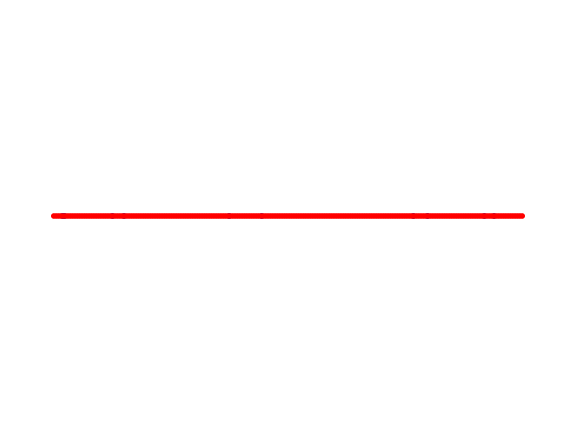

```mathematica
sim=With[{particlenum = 10,recepcol=200, receptordist = 0.03466, nSteps=10000},

Module[{widthsim = recepcol*receptordist,receptors, nodalligand,nodalstruct, receptorstruct, receptorpts,temp, boundn,boundl,g,nodtracklist,nodinlist,clistnod,clistleft,clistn,pos},

receptors=Table[{i,0},{i,receptordist/2,widthsim,receptordist}];

nodalligand=  RandomPoint[Subscript[ℛ, 2],particlenum];

Print@Graphics[{Subscript[ℛ, 2],PointSize[0.007],Darker@Blue,Point@nodalligand,Red,Point@receptors},ImageSize->Large];

nodalstruct = Association@MapIndexed[#2[[1]]-> {"nodal",#1}&,nodalligand];
receptorstruct = MapIndexed[#2[[1]]-> {#1,0,None,None}&,receptors];
receptorpts = (Values@receptorstruct)[[All,1]];


clistnod = ConstantArray[{0,0},particlenum];
clistleft = ConstantArray[{0,0},particlenum];

Monitor[Reap[
Nest[(temp = BrownianSimulation@@#;
boundn = Cases[temp[[1]],patt:PatternSequence[_-> {{_,_},_,_,"nodal" }]:> {patt[[2,3]],patt[[2,1]]},2];boundl = Cases[temp[[1]],patt:PatternSequence[_-> {{_,_},_,_,"lefty" }]:> {patt[[2,3]],patt[[2,1]]},2];

nodinlist=temp[[3]];

If[nodinlist=== {},(nodtracklist=Sort@boundn),
(nodtracklist=Sort@Join[boundn,nodinlist/.patt:{_Integer,{_,_}}/;Head[patt]=!=List :> {patt}])];

g =graphState[receptors,nodinlist[[All,2]],{},boundn[[All,2]],boundl];

clistn= temp[[-2]];
pos=Flatten@Position[clistn,Except[{0,0}],1][[2;;All]];

If[Length@pos>0,
nodtracklist=ReplacePart[nodtracklist,Thread[pos-> Thread[pos-> Map[nodtracklist[[#]][[2]] + clistn[[#]]*widthsim&,pos]]]]
,nodtracklist];

Sow[nodtracklist];

temp[[3]] = Association@Map[#[[1]]-> {"nodal",#[[2]]}&,temp[[3]]];
temp[[4]] = <||>;
temp)&, {receptorstruct,receptorpts,nodalstruct,<||>,clistnod,clistleft},nSteps]]
,g]//Quiet
]
];
```

## checking Absolute Coordinates for particles

```mathematica
absCoordCheck[simres_]:= Module[{listpcrossed,particlecrossed},
listpcrossed = simres[[1]][[-2]];
particlecrossed = Flatten[Position[listpcrossed,Except[{0,0}],{1}]/.{0}:> Sequence[]];
Transpose[{particlecrossed,listpcrossed[[particlecrossed]]}]
]
```

```mathematica
absCoordCheck[sim]
```

{{2,{-1,0}}}

```mathematica
tagged=GroupBy[#,First]&@ Flatten[First@sim[[-1]],1];
```

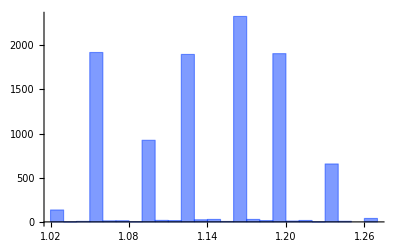
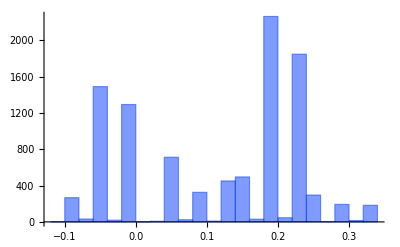
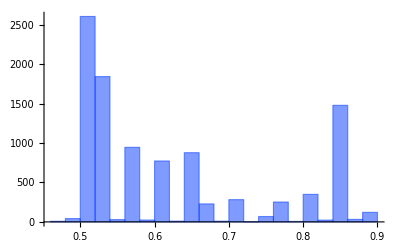
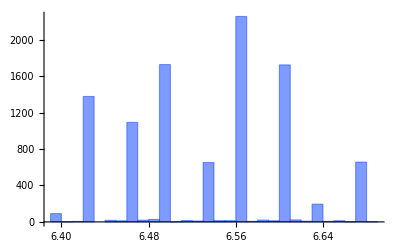
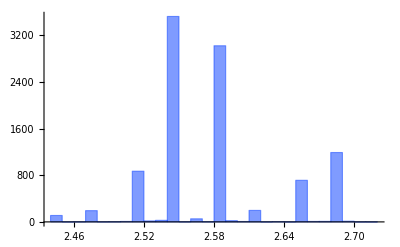
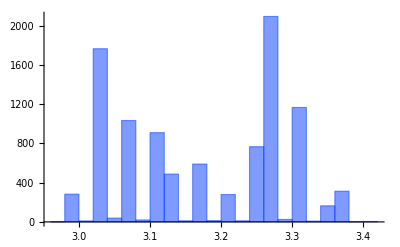
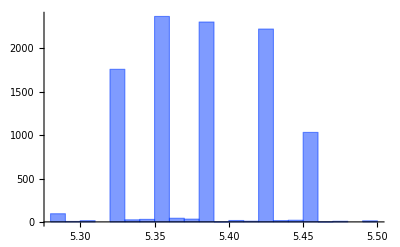
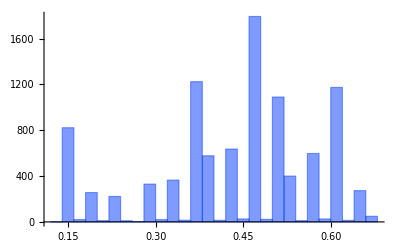

```mathematica
Map[Function[x,(tagged[[x]][[All,2]][[All,1]]//Histogram[#,ChartStyle->XYZColor[0,0,1,0.5]]&)],Range[10]]
```

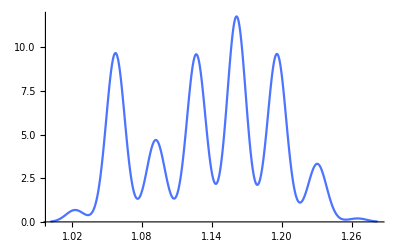
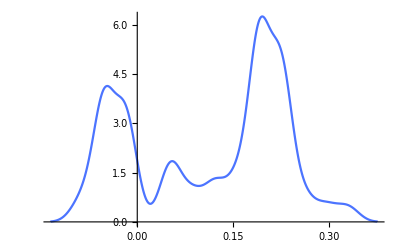
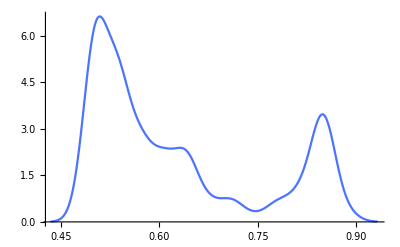
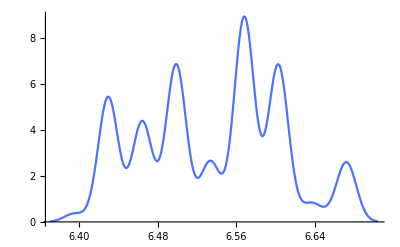
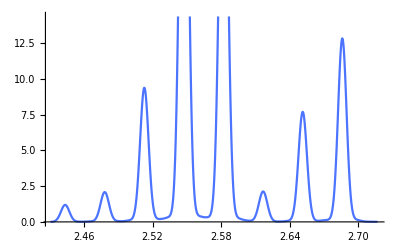
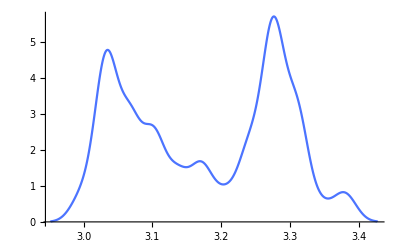
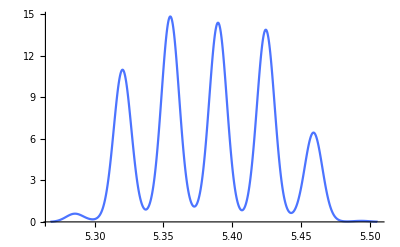
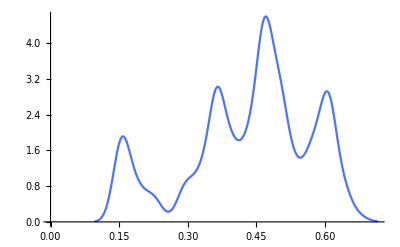

```mathematica
Map[Function[x,(tagged[[x]][[All,2]][[All,1]]//SmoothHistogram[#,PlotStyle->XYZColor[{0,0,1,0.7}]]&)],Range[10]]
```

## Analysis

```mathematica
stateDraw[tag_,parnum_]:= Module[{data,boundones,boundonesnoInd,boundonesindexed},
data = Table[
Module[{series,totaltimeboundunbound,timesbound,numtimestepbound}, 
series= tag[[i]][[All,2]][[All,1]];
totaltimeboundunbound=(Differences@series)/. {0.:> 0,_Real:> 1}//Counts;
timesbound=(Differences@series)/.{0.:> 0,_Real:> 1}//Split//Count[#,Repeated[{0..}]]&;
numtimestepbound = Map[Length,(Differences@series)/.{0.:> 0,_Real:> 1}//Split//Cases[#,{0..}]&];
{totaltimeboundunbound,timesbound,numtimestepbound}
],{i,parnum}];

boundones = Replace[data,patt:PatternSequence[{_?AssociationQ,_,{}}]:> Sequence[],1];
boundonesnoInd =boundones[[All,3]];
boundonesindexed=MapIndexed[Thread[{#2[[1]],boundonesnoInd[[#]]}]&,Range[Length@boundones]];

GraphicsColumn@{ListPlot[boundonesindexed,PlotStyle-> {Blue},PlotLabel -> Style[#,{Bold,FontSize->12,Black}]&@"number of times ligand bound vs how long it remained bound",AxesLabel->{"# of times bound","How long? (# of δt bound)"},ImageSize->Large],GraphicsRow@{Histogram[Flatten@boundones[[All,3]],PlotRange->All,ChartStyle->{XYZColor[0,0,5,0.2]},PlotLabel->Style[#,{Bold,FontSize->12,Black}]&@"counts of stay",ImageSize->Medium],
Histogram[Flatten@boundones[[All,3]],Automatic,"Probability",PlotRange->All,ChartStyle->{XYZColor[0,0,5,0.2]},PlotLabel->Style[#,{Bold,FontSize->12,Black}]&@"probability of stay",ImageSize->Medium]}}
]
```

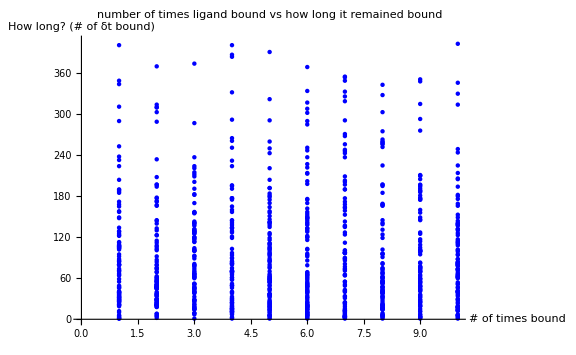

```mathematica
stateDraw[tagged,10]
```

```mathematica
list = <|MapIndexed[#2[[1]]-> #[[2]][[All,2]][[All,1]]&,(tagged/.Association-> List)]|>;
```

### MeanSquareDisplacement in 1D

```mathematica
dx=With[{parnum=10,timesteps=1000},
Module[{transposedlist,length},
transposedlist=Transpose@Table[
Thread[{list[[j]],RotateLeft[list[[j]],i]}][[;;-(i+1)]]
,{j,parnum},{i,timesteps}];

length=(Dimensions/@transposedlist)[[All,2]];

Table[
Module[{listreshape,lx},
listreshape=ArrayReshape[transposedlist[[i]],{parnum*length[[i]],1,2}];
Mean@Flatten[Map[Function[x,Power[#,2]&@Differences@(Reverse@@x)],listreshape],1]
],{i,timesteps}]
]
];
```

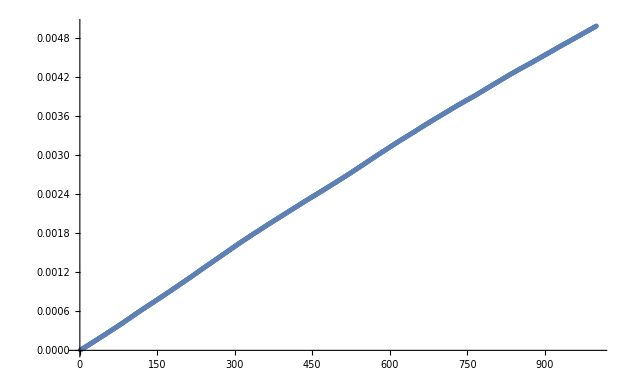

```mathematica
ListPlot@dx
```

```mathematica
grad = LinearModelFit[dx[[1;;100]],{x},x]
```

FittedModel[-4.87419×10^-6+5.14331×10^-6 x]

```mathematica
grad[[1]][[2]][[-1]]/(2* 1 10^-6)
```

2.57165